```mathematica
ClearAll["Global`*"]
$Assumptions= τ ∈ Reals && m∈Reals && n ∈ Reals &&r ∈Reals&& τ>0;
alpha[m_,n_]:= 1/2 KroneckerDelta[0, Abs[m-n]] - 1/4 KroneckerDelta[1, Abs[m-n]] + E^(-(m-n)^2/ 8/Pi/ξ /ξ )/2/Sqrt[2]/Pi/ξ ;
beta [m_,n_]:= Sign[m-n]* ( 1/4 KroneckerDelta[1, Abs[m-n]] - Exp[I*(2τ- Abs[m-n]^2/4/ξ/l)]/2/Sqrt[π ξ l] Exp[- π Abs[m-n]^2/4/l/l ]Sqrt[1-Exp[-π Abs[m-n]^2/4/l/l]]           );
ξ= Sqrt[τ];
l = Sqrt[τ]* Log[τ];
BA[m_,n_]:=KroneckerDelta[m,n]-2alpha[n-m,0]+2Re[beta[n-m,0]];
G [n_]:= Simplify[BA[0,n+1]]
```

```mathematica
(*You must have D[Nd_,tau_] defined elsewhere;this uses it as given.*)ClearAll[removeDuplicatesInPairs,sigmaGeneral];

removeDuplicatesInPairs[vec_List]:=Module[{c=Counts[vec]},(*keep values that occur an odd number of times*)Select[Keys[c],OddQ[c[#]]&]];

sigmaGeneral[indices_List]:=Module[{idx,oddSites,evenSites,jwLens,n,r,aCoords,bCoords,cMat},(*Sigma matrices on different sites commute;sort indices*)idx=Sort[indices];
(*remove duplicates since sigma_x^2=1*)idx=removeDuplicatesInPairs[idx];
(*require pairs*)If[OddQ[Length[idx]],Return[$Failed]];
(*Bs sit on odd positions in the (paired) list;As on even positions*)oddSites=idx[[1;; ;;2]];
evenSites=idx[[2;; ;;2]];
(*string lengths*)jwLens=evenSites-oddSites;
(*matrix size*)n=Total[jwLens];
(*fill in indices for strings:for each pair (start,end),include start..end*)r=Flatten@Table[Range[idx[[i]],idx[[i+1]]],{i,1,Length[idx],2}];
aCoords=Complement[r,oddSites];
bCoords=Complement[r,evenSites];
cMat=Table[Module[{Bx=bCoords[[nx]],Ay=aCoords[[ny]],Nd},Nd=Bx-Ay+1;
G[Nd]],{nx,1,n},{ny,1,n}];
Det[cMat]];
(************************************************
*PROJECTORS************************************************)(*Assumes sigmaGeneral[indices_] or sigmaGeneral[indices_,___] is defined elsewhere,but Pn itself has no tau dependence*)ClearAll[binomialExpansion,allCombinations,uniqueElementsAndFrequencies,Pn];

(*Computes all pairs of combinations of indices*)
binomialExpansion[indices_List]:=Subsets[indices,{2}];

(*Computes all combinations of all lengths of indices*)
allCombinations[indices_List]:=Flatten[Table[Subsets[indices,{r}],{r,0,Length[indices]}],1];

(*Unique elements and their frequencies*)
uniqueElementsAndFrequencies[vec_List]:=Tally[vec];

Pn[n_Integer,even_:True]:=Module[{indices,terms,xc,counter,vecs,counts,dat,term,idx,degen},(*For most cases we use periodic boundary conditions*)(*That said,watch out for this definition of indices*)indices=Range[0,n-1];
terms=allCombinations[indices];
(*shift each non-empty combination by its first element*)xc=Table[With[{a=terms[[i]]},If[a==={},Nothing,a-First[a]]],{i,2,Length[terms]}];
counter=Tally[xc];
vecs=counter[[All,1]];
counts=counter[[All,2]];
dat=Table[idx=vecs[[term]];
degen=counts[[term]];
If[OddQ[Length[idx]],If[even===True,0,((*odd-sector contribution,kept for completeness*)idx=Join[idx,idx+Floor[Length[idx]/2]];
Sqrt[Abs[sigmaGeneral[idx]]]*degen)],sigmaGeneral[idx]*degen],{term,Length[vecs]}];
(*Manually add the identity term*)AppendTo[dat,1];
(*All terms have equal weight*)Total[dat]/2^n];
```

```mathematica
aPn[n_] :=Asymptotic[ 1/2 - Pn[n],τ->Infinity]
```

```mathematica
dat={aPn[2],aPn[3]}
```

{1/(4 √2 π √τ),1/(2 √2 π √τ)}

```mathematica
Simplify[Asymptotic[x,τ->Infinity]]
```

x

```mathematica
x=Asymptotic[1-sigmaGeneral[{0,1,4,5}],τ->Infinity]
y= Asymptotic[1-sigmaGeneral[{0,1}],τ->Infinity]
x/y
```

(√2)/(π √τ)

1/(√2 π √τ)

2

```mathematica
aP2 = Simplify[1/2 - Pn[2]]
```

((√2 ⅇ^(-1/(8 π τ)))/(√τ)+2 √π Re[(ⅇ^(-(π+ⅈ Log[τ]-8 ⅈ τ^2 Log[τ]^2)/(4 τ Log[τ]^2)) √(1-ⅇ^(-π/(4 τ Log[τ]^2))))/(√(τ Log[τ]))])/(8 π)

```mathematica
y=((√2 ⅇ^(-1/(8 π τ)))/(√τ))/(8 π);
```

```mathematica
Series[y,{τ,∞,4}]
```

(√(1/τ))/(4 √2 π)-(1/τ)^(3/2)/(32 (√2 π^2))+(1/τ)^(5/2)/(512 √2 π^3)-(1/τ)^(7/2)/(12288 (√2 π^4))+O[1/τ]^(9/2)

```mathematica
2
```

```mathematica
z=Simplify[((√2 ⅇ^(-1/(8 π τ)))/(√τ)+2 √π Re[(ⅇ^(-(π+ⅈ Log[τ]-8 ⅈ τ^2 Log[τ]^2)/(4 τ Log[τ]^2)) √(1-ⅇ^(-π/(4 τ Log[τ]^2))))/(√(τ Log[τ]))])/(8 π)-y]
```

```mathematica
z=(ⅇ^(-(π+ⅈ Log[τ]-8 ⅈ τ^2 Log[τ]^2)/(4 τ Log[τ]^2)) √(1-ⅇ^(-π/(4 τ Log[τ]^2))))/(√(τ Log[τ]))
```

(ⅇ^(-(π+ⅈ Log[τ]-8 ⅈ τ^2 Log[τ]^2)/(4 τ Log[τ]^2)) √(1-ⅇ^(-π/(4 τ Log[τ]^2))))/(√(τ Log[τ]))

```mathematica
Series[z,{τ,∞,3}]
```

ⅇ^(2 ⅈ τ+(-π-ⅈ Log[τ])/(4 Log[τ]^2 τ)+O[1/τ]^4) ((√π)/(2 Log[τ]^(3/2) τ)-π^(3/2)/(32 Log[τ]^(7/2) τ^2)+(5 π^(5/2))/(3072 Log[τ]^(11/2) τ^3)+O[1/τ]^4)

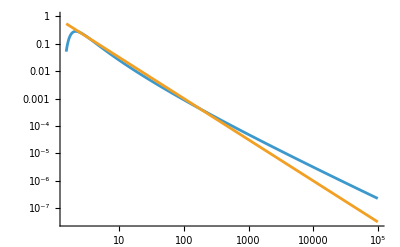

```mathematica
LogLogPlot[{Abs[z],τ^-(3/2)},{τ,1.5,100000}]
```

```mathematica
expr=((Sqrt[2] Exp[-1/(8 Pi τ)])/Sqrt[τ]+2 Sqrt[Pi] Re[Exp[-((Pi+I Log[τ]-8 I τ^2 Log[τ]^2)/(4 τ Log[τ]^2))]*Sqrt[1-Exp[-(Pi/(4 τ Log[τ]^2))]]]/Sqrt[τ Log[τ]])/(8 Pi);

FullSimplify[Assuming[τ>0,FullSimplify[ComplexExpand[expr]]]]
```

1/(8 π τ)(√2 ⅇ^(-1/(8 π τ)) √τ+1/(√Abs[Log[τ]])2 ⅇ^(-1/2 ⅈ Arg[Log[τ]]-π/(4 τ Log[τ]^2)) √π (ⅇ^(-π/(2 τ Log[τ]^2)) (-1+ⅇ^(π/(4 τ Log[τ]^2)))^2 τ^2)^(1/4) Cos[2 τ+1/2 Arg[1-ⅇ^(-π/(4 τ Log[τ]^2))]-1/(4 τ Log[τ])])

```mathematica
Series[expr,{τ,∞,2}]
```

Re[ⅇ^(2 ⅈ τ+(-π-ⅈ Log[τ])/(4 Log[τ]^2 τ)+O[1/τ]^3)] (1/(8 Log[τ]^(3/2) τ)-π/(128 Log[τ]^(7/2) τ^2)+O[1/τ]^3)+((√(1/τ))/(4 √2 π)-(1/τ)^(3/2)/(32 (√2 π^2))+O[1/τ]^(5/2))

```mathematica
ap[n_] := FullSimplify[1/2- Pn[n]]
```

```mathematica
ap[3]
```

1/(16 π^2 τ)ⅇ^(-1/(2 π τ)) (1-ⅇ^(1/(4 π τ))+4 √2 ⅇ^(3/(8 π τ)) π √τ+ⅇ^(1/(2 π τ)) √(2 π) Re[(ⅇ^((-π+ⅈ Log[τ] (-1+2 τ^2 Log[τ]))/(τ Log[τ]^2)) √(1-ⅇ^(-π/(τ Log[τ]^2))))/(√Log[τ])]-2 ⅇ^(3/(8 π τ)) √π Re[(ⅇ^(-(π+ⅈ Log[τ] (1-8 τ^2 Log[τ]))/(4 τ Log[τ]^2)) √(1-ⅇ^(-π/(4 τ Log[τ]^2))))/(√Log[τ])] (√2+ⅇ^(1/(8 π τ)) √π (-4 √π √τ+Re[(ⅇ^(-(π+ⅈ Log[τ] (1-8 τ^2 Log[τ]))/(4 τ Log[τ]^2)) √(1-ⅇ^(-π/(4 τ Log[τ]^2))))/(√Log[τ])])))

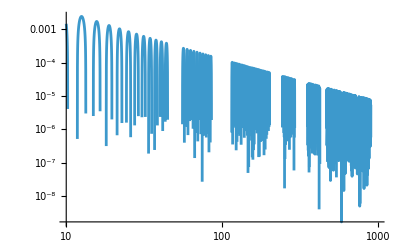

```mathematica
LogLogPlot[Re[ⅇ^(2 ⅈ τ+(-π-ⅈ Log[τ])/(4 τ Log[τ]^2))]/(8 τ Log[τ]^(3/2)),{τ,10,1000}]
```

Re[ⅇ^(2 ⅈ τ-ⅈ/(τ Log[τ]))]

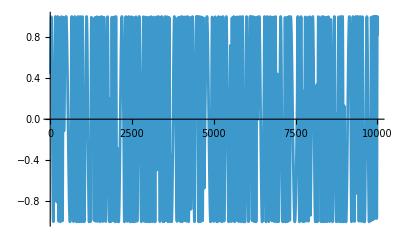

```mathematica
Re[E^(2I τ-I/τ/Log[τ])]
```

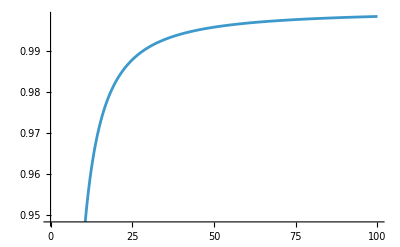

```mathematica
Plot[ⅇ^(-π/(τ Log[τ]^2)),{τ,0,100}]
```

```mathematica
ap2=Simplify[1/2-Pn[2]]
```

((√2 ⅇ^(-1/(8 π τ)))/(√τ)+2 √π Re[(ⅇ^(-(π+ⅈ Log[τ]-8 ⅈ τ^2 Log[τ]^2)/(4 τ Log[τ]^2)) √(1-ⅇ^(-π/(4 τ Log[τ]^2))))/(√(τ Log[τ]))])/(8 π)

```mathematica
Normal[Series[ap2,{τ,∞,2}]]
```

-1/(32 √2 π^2 τ^(3/2))+1/(4 √2 π √τ)+(-π/(128 τ^2 Log[τ]^(7/2))+1/(8 τ Log[τ]^(3/2))) Re[ⅇ^(2 ⅈ τ+(-π-ⅈ Log[τ])/(4 τ Log[τ]^2))]

```mathematica
Series[Simplify[-1/(32 √2 π^2 τ^(3/2))+1/(4 √2 π √τ)+(-π/(128 τ^2 Log[τ]^(7/2))+1/(8 τ Log[τ]^(3/2)))],{ τ,∞,2}]
```

(√(1/τ))/(4 √2 π)+1/(8 Log[τ]^(3/2) τ)-(1/τ)^(3/2)/(32 (√2 π^2))-π/(128 Log[τ]^(7/2) τ^2)+O[1/τ]^(5/2)

```mathematica
1
```